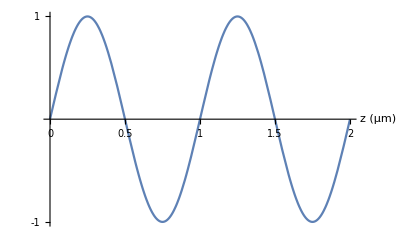

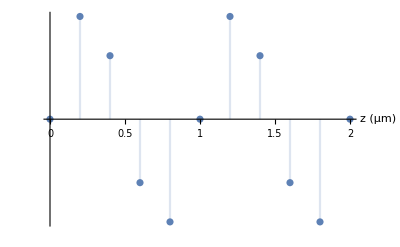

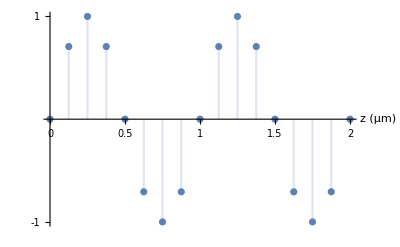

```mathematica
Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"z (μm)", None},AxesStyle->Directive["Label", 16]]
DiscretePlot[Sin[2π t],{t,0,2,0.2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"z (μm)", None},AxesStyle->Directive["Label", 16]]
DiscretePlot[Sin[2π t],{t,0,2,0.125},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"z (μm)", None},AxesStyle->Directive["Label", 16]]
```

```mathematica
UnitConvert[5*(1.μm)/c,fs]
```

16.6782 fs

```mathematica
UnitConvert[0.5/10*(0.3μm)/c,fs]
```

0.0500346 fs

```mathematica
0.5/16.
```

0.03125

```mathematica
5/0.03125
```

160.

```mathematica
1/16.
```

0.0625

```mathematica
1.4^2
```

1.96

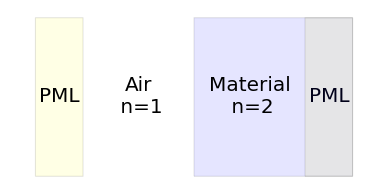

```mathematica
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{0,0},{3,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1]},Yellow],
Style[Rectangle[{17,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Yellow}],
Rotate[Text[Style["PML",FontSize->20],{1.5,5}],90°],
Rotate[Text[Style["PML",FontSize->20],{18.5,5}],90°],
Style[Rectangle[{3,0},{10,10}],{EdgeForm[{Dashed, Black}],Opacity[0],White}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Text[Style["Air\n n=1",FontSize->20],{6.5,5}],
Text[Style["Material\n n=2",FontSize->20],{13.5,5}]
}]
```

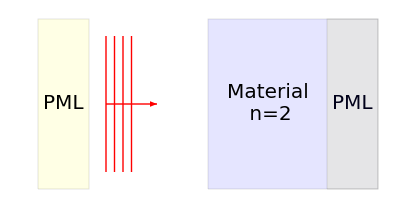

```mathematica
Graphics[{
Style[Line[{{5,1},{5,9}}],Red],
Style[Line[{{4.5,1},{4.5,9}}],Red],
Style[Line[{{4,1},{4,9}}],Red],
Style[Line[{{5.5,1},{5.5,9}}],Red],
Style[Arrow[{{4,5},{7,5}}],Red,Thick],
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{0,0},{3,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1]},Yellow],
Style[Rectangle[{17,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Yellow}],
Rotate[Text[Style["PML",FontSize->20],{1.5,5}],90°],
Rotate[Text[Style["PML",FontSize->20],{18.5,5}],90°],
Style[Rectangle[{3,0},{10,10}],{EdgeForm[{Dashed, Black}],Opacity[0],White}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Text[Style["Material\n n=2",FontSize->20],{13.5,5}]
}]
```

```mathematica
0.667*0.5
```

0.3335

```mathematica
1/3+0.5
```

0.833333

```mathematica
((1-2)/(1+2))^2
```

1/9

```mathematica
8./9
```

0.888889

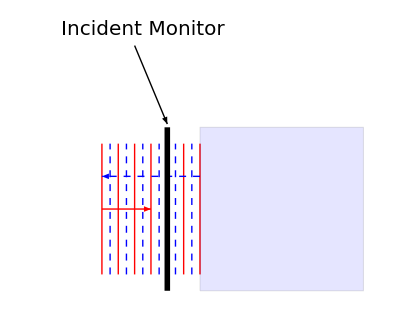

```mathematica
Graphics[{
Table[Style[Line[{{n,1},{n,9}}],Red],{n,4.,10,1}],
Table[Style[Line[{{n,1},{n,9}}],Blue,Dashed],{n,4.5,10,1}],
Style[Arrow[{{4,5},{7,5}}],Red,Thick],
Style[Arrow[{{10,7},{4,7}}],Blue,Dashed],
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Style[Line[{{8,0},{8,10}}],Thickness[0.01]],
Arrow[{{6,15},{8,10.2}}],
Text[Style["Incident Monitor",FontSize->20],{6.5,16}]
}]
```

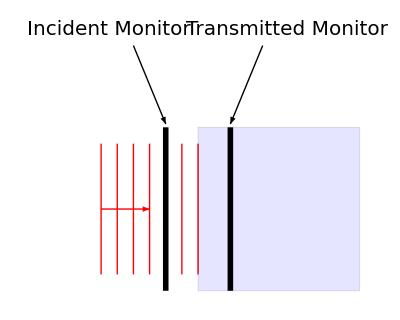

```mathematica
Graphics[{
Table[Style[Line[{{n,1},{n,9}}],Red],{n,4.,10,1}],
Style[Arrow[{{4,5},{7,5}}],Red,Thick],
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Style[Line[{{12,0},{12,10}}],Thickness[0.01]],
Arrow[{{14,15},{12,10.2}}],
Text[Style["Transmitted Monitor",FontSize->20],{15.5,16}],
Arrow[{{6,15},{8,10.2}}],
Text[Style["Incident Monitor",FontSize->20],{4.5,16}],
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Line[{{8,0},{8,10}}],Thickness[0.01]],
}]
```

```mathematica
m ww
```

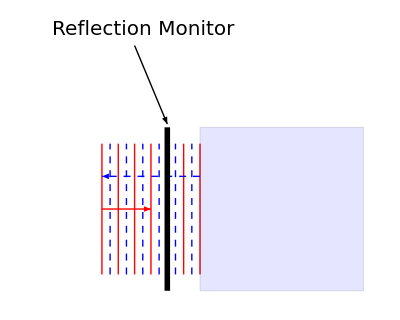

```mathematica
Graphics[{
Table[Style[Line[{{n,1},{n,9}}],Red],{n,4.,10,1}],
Table[Style[Line[{{n,1},{n,9}}],Blue,Dashed],{n,4.5,10,1}],
Style[Arrow[{{4,5},{7,5}}],Red,Thick],
Style[Arrow[{{10,7},{4,7}}],Blue,Dashed],
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Style[Line[{{8,0},{8,10}}],Thickness[0.01]],
Arrow[{{6,15},{8,10.2}}],
Text[Style["Reflection Monitor",FontSize->20],{6.5,16}]
}]
```

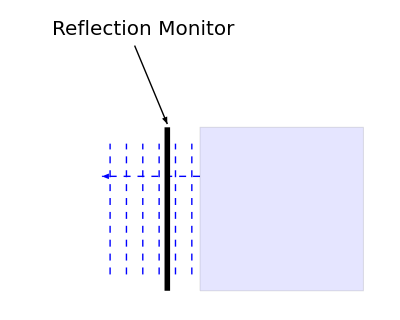

```mathematica
Graphics[{
Table[Style[Line[{{n,1},{n,9}}],Blue,Dashed],{n,4.5,10,1}],
Style[Arrow[{{10,7},{4,7}}],Blue,Dashed],
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Style[Line[{{8,0},{8,10}}],Thickness[0.01]],
Arrow[{{6,15},{8,10.2}}],
Text[Style["Reflection Monitor",FontSize->20],{6.5,16}]
}]
```

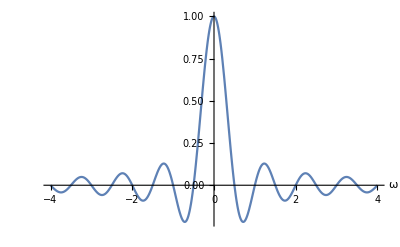

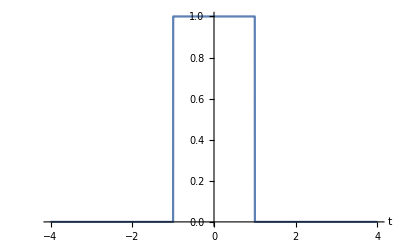

```mathematica
plot1=Plot[Sinc[2π t],{t,-4,4},Ticks->None,TicksStyle->Directive["Label", 14],AxesLabel->{"ω", None},AxesStyle->Directive["Label", 16],PlotRange->Full]
plot2=Plot[UnitStep[t+1]-UnitStep[t-1],{t,-4,4},Ticks->None,TicksStyle->Directive["Label", 14],AxesLabel->{"t", None},AxesStyle->Directive["Label", 16],PlotRange->Full,Exclusions->None]
```

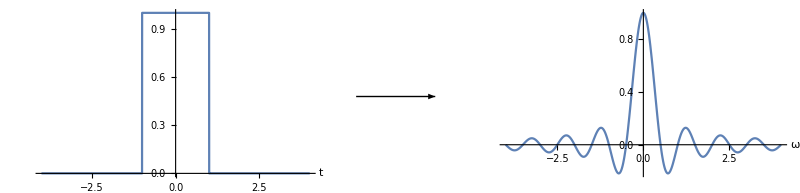

```mathematica
GraphicsRow[{plot2,arrow,plot1}]
```

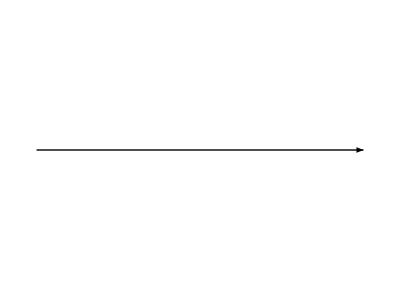

```mathematica
arrow=Graphics[{Arrowheads[.4],Arrow[{{0,0},{0.5,0}}]}]
```

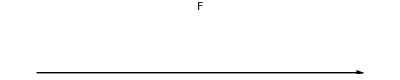

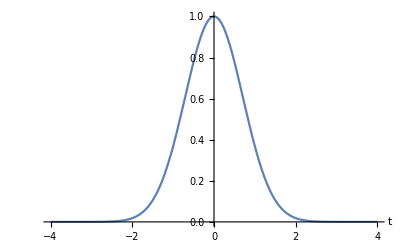

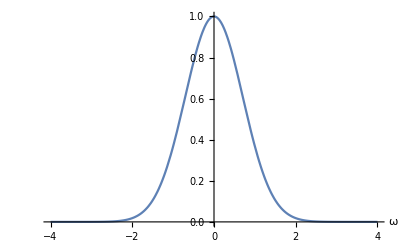

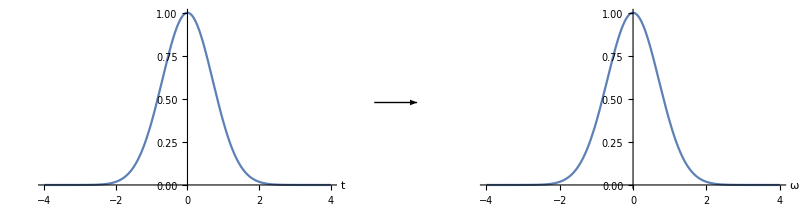

```mathematica
plot1=Plot[ⅇ^(-t^2),{t,-4,4},Ticks->None,TicksStyle->Directive["Label", 14],AxesLabel->{"t", None},AxesStyle->Directive["Label", 16],PlotRange->Full]
plot2=Plot[ⅇ^(-t^2),{t,-4,4},Ticks->None,TicksStyle->Directive["Label", 14],AxesLabel->{"ω", None},AxesStyle->Directive["Label", 16],PlotRange->Full,Exclusions->None]
GraphicsRow[{plot1,arrow,plot2}]
```

```mathematica
Δt={{8,0.91863619-0.89896906},{16,0.89576823-0.89173868},{32,0.89057291-0.88949312},{64,0.88930785-0.88903957},{128,0.88899349-0.88892653},{256,0.88891502-0.88889828}}
Terr={{8,0.91863619-8/9},{16,0.89576823-8/9},{32,0.89057291-8/9},{64,0.88930785-8/9},{128,0.88899349-8/9},{256,0.88891502-8/9}}
```

{{8,0.0196671},{16,0.00402955},{32,0.00107979},{64,0.00026828},{128,0.00006696},{256,0.00001674}}

{{8,0.0297473},{16,0.00687934},{32,0.00168402},{64,0.000418961},{128,0.000104601},{256,0.0000261311}}

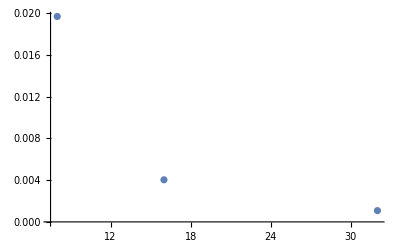

```mathematica
ListPlot[Δr]
```

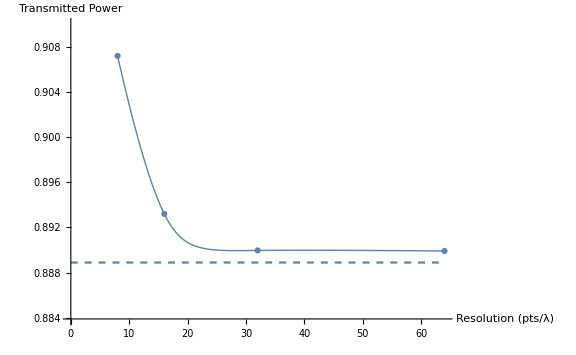

```mathematica
Show[{ListPlot[{{8, 0.9072},{16, 0.8932},{32, 0.88996},{64,0.88991}},Joined->True,InterpolationOrder->3,AxesLabel->{"Resolution (pts/λ)","Transmitted Power"},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotStyle->Thick,PlotMarkers->{Automatic},PlotRange->{8/9.-0.005,0.91},ImageSize->Large],Plot[8/9.,{x,0,64},PlotStyle->Dashed,ImageSize->Large]}]
```

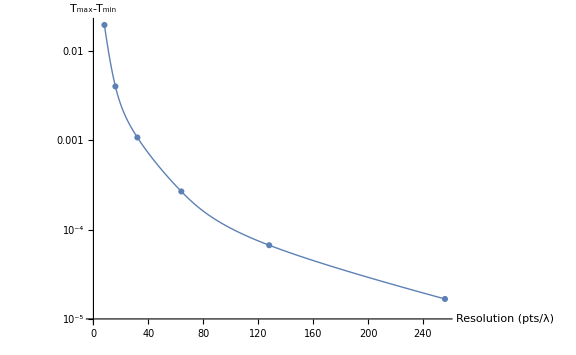

```mathematica
ListLogPlot[Δt,Joined->True,InterpolationOrder->3,AxesLabel->{"Resolution (pts/λ)","T_max-T_min"},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotStyle->Thick,PlotMarkers->{Automatic},PlotRange->{10^-5,0.02},ImageSize->Large]
```

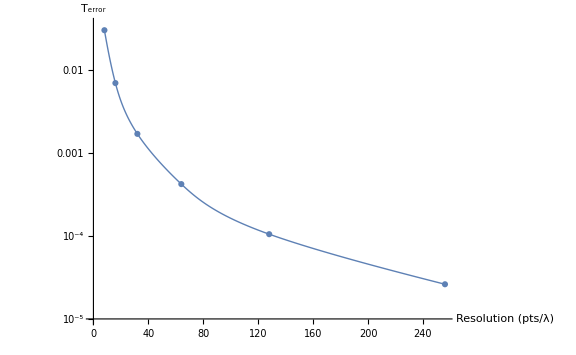

```mathematica
ListLogPlot[Terr,Joined->True,InterpolationOrder->3,AxesLabel->{"Resolution (pts/λ)","T_error"},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotStyle->Thick,PlotMarkers->{Automatic},PlotRange->{10^-5,0.035},ImageSize->Large]
```

```mathematica
sinData={{0.2066,1.01},{0.2101,1.083},{0.2138,1.133},{0.2175,1.186},{0.2214,1.247},{0.2254,1.34},{0.2296,1.471},{0.2339,1.579},{0.2384,1.589},{0.2431,1.571},{0.248,1.57},{0.253,1.597},{0.2583,1.658},{0.2638,1.764},{0.2695,1.988},{0.2755,2.452},{0.2818,3.12},{0.2883,4.087},{0.2952,4.888},{0.3024,5.02},{0.31,5.01},{0.3179,5.016},{0.3263,5.065},{0.3351,5.156},{0.3444,5.296},{0.3542,5.61},{0.3647,6.522},{0.3757,6.709},{0.3875,6.062},{0.3999,5.57},{0.4133,5.222},{0.4275,4.961},{0.4428,4.753},{0.4592,4.583},{0.4769,4.442},{0.4959,4.32},{0.5166,4.215},{0.5391,4.123},{0.5636,4.042},{0.5904,3.969},{0.6199,3.906},{0.6525,3.847},{0.6888,3.796},{0.7293,3.752},{0.7749,3.714},{0.8266,3.673}}
```

{{0.2066,1.01},{0.2101,1.083},{0.2138,1.133},{0.2175,1.186},{0.2214,1.247},{0.2254,1.34},{0.2296,1.471},{0.2339,1.579},{0.2384,1.589},{0.2431,1.571},{0.248,1.57},{0.253,1.597},{0.2583,1.658},{0.2638,1.764},{0.2695,1.988},{0.2755,2.452},{0.2818,3.12},{0.2883,4.087},{0.2952,4.888},{0.3024,5.02},{0.31,5.01},{0.3179,5.016},{0.3263,5.065},{0.3351,5.156},{0.3444,5.296},{0.3542,5.61},{0.3647,6.522},{0.3757,6.709},{0.3875,6.062},{0.3999,5.57},{0.4133,5.222},{0.4275,4.961},{0.4428,4.753},{0.4592,4.583},{0.4769,4.442},{0.4959,4.32},{0.5166,4.215},{0.5391,4.123},{0.5636,4.042},{0.5904,3.969},{0.6199,3.906},{0.6525,3.847},{0.6888,3.796},{0.7293,3.752},{0.7749,3.714},{0.8266,3.673}}

```mathematica
siData[[1,1]]-1
```

-0.7934

```mathematica
ListPlot[siData]
```

ListPlot::lpn: {{{1.,0.2066},{2.,1.01}},{{1.,0.2101},{2.,1.083}},{{1.,0.2138},{2.,1.133}},{{1.,0.2175},{2.,1.186}},{{1.,0.2214},{2.,1.247}},{{1.,0.2254},{2.,1.34}},«39»,{{1.,0.8266},{2.,3.673}},{},{{1.,wl},{2.,k}},{{1.,0.2066},{2.,2.909}},{{1.,0.2101},{2.,2.982}},«44»} is not a list of numbers or pairs of numbers.

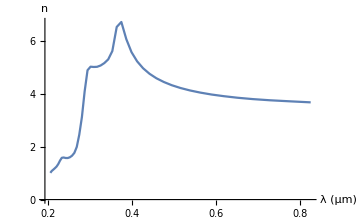

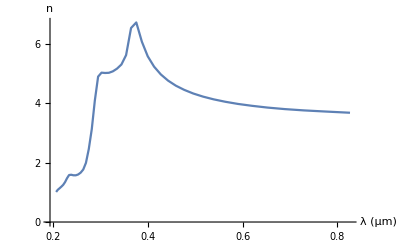

```mathematica
ListPlot[sinData,Ticks->{{0.2,0.3,0.4,0.5,0.6,0.7,0.8},{0,1,2,3,4,5,6,7}},TicksStyle->Directive["Label", 14],AxesLabel->{"λ (μm)", "n"},AxesStyle->Directive["Label", 16],Joined->True,ImageSize->Medium]
```

```mathematica
8*1/(0.5/8)
```

128.

```mathematica
1/2.5
```

0.4

```mathematica
((1-4)/(1+4))^2//N
```

0.36

```mathematica
ArcTan[2.]*180/π
```

63.4349

{Arrow[{{0,0},{3,0}}],Arrow[{{0,0},{0,3}}],Circle[{0,0},0.5],Disk[{0,0},0.2]}

{Arrow[{{0,0},{3,0}}],Arrow[{{0,0},{0,3}}],Circle[{0,0},0.5],Disk[{0,0},0.2]}

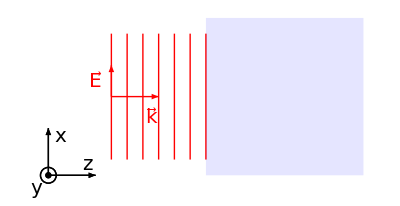

```mathematica
axesYInward={Style[Arrow[{{0,0},{3,0}}],Black,Thick],
Style[Arrow[{{0,0},{0,3}}],Black,Thick],
Style[Circle[{0,0},0.5]],
Style[Disk[{0,0},0.2]],
Text[Style["z",FontSize->20],{2.5,0.75}],
Text[Style["x",FontSize->20],{0.75,2.5}],
Text[Style["y",FontSize->20],{-0.75,-0.75}]
};
axesYBare={Style[Arrow[{{0,0},{3,0}}],Black,Thick],
Style[Arrow[{{0,0},{0,3}}],Black,Thick],
Style[Circle[{0,0},0.5]],
Style[Disk[{0,0},0.2]]}
Graphics[{
Table[Style[Line[{{n,1},{n,9}}],Red],{n,4.,10,1}],
Style[Arrow[{{4,5},{7,5}}],Red,Thick],
Style[Arrow[{{4,5},{4,7}}],Red,Thick],
Text[Style[OverVector["k"],FontSize->20,Red],{6.5,3.75}],
Text[Style[OverVector["E"],FontSize->20,Red],{3,6}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[None],Opacity[0.1],Blue}],
Style[Arrow[{{0,0},{3,0}}],Black,Thick],
Style[Arrow[{{0,0},{0,3}}],Black,Thick],
Style[Circle[{0,0},0.5]],
Style[Disk[{0,0},0.2]],axesYInward
}]
```

```mathematica
OverVector["E"]
```

E⃗

```mathematica
Graphics[{
Rotate[{Table[Style[Line[{{n,1},{n,9}}],Red],{n,4.,10,1}],Style[Arrow[{{4,5},{7,5}}],Red,Thick],
Style[Arrow[{{4,5},{4,7}}],Red,Thick],
Text[Style[OverVector["k"],FontSize->20,Red],{6.5,3.75}],
Text[Style[OverVector["E"],FontSize->20,Red],{3,6}]},30°],
Style[Line[{{4,3.8},{10,3.8}}],Dashed],
Style[Circle[{4,3.8},2,{0,π/6}],Thick],
Text[Style["θ",FontSize->20,Black],{6.25,3}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[None],Opacity[0.1],Blue}],
Style[Arrow[{{0,0},{3,0}}],Black,Thick],
Style[Arrow[{{0,0},{0,3}}],Black,Thick],
Style[Circle[{0,0},0.5]],
Style[Disk[{0,0},0.2]],axesYInward
}]
```

-Graphics-

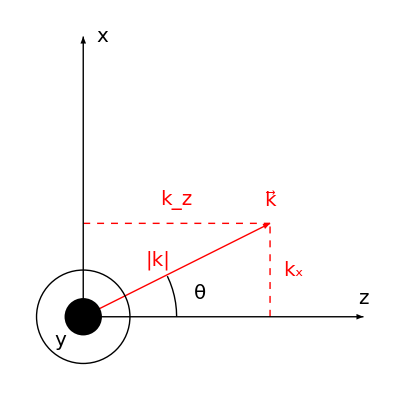

```mathematica
Graphics[{
Text[Style[OverVector["k"],FontSize->20,Red],{2,1.25}],
Text[Style["k_z",FontSize->20,Red],{1,1.25}],
Text[Style["k_x",FontSize->20,Red],{2.25,0.5}],
Text[Style["|k|",FontSize->20,Red],{0.8,0.6}],
Style[Arrow[{{0,0},{2,1}}],Red],
Style[Line[{{0,1},{2,1}}],Dashed,Red],
Style[Line[{{2,0},{2,1}}],Dashed,Red],
Text[Style["z",FontSize->20],{3.,0.2}],
Text[Style["x",FontSize->20],{0.2,3}],
Text[Style["y",FontSize->20],{-0.25,-0.25}],
Style[Circle[{0,0},1,{0,0.45}],Thick],
Text[Style["θ",FontSize->20,Black],{1.25,0.25}],
axesYBare}]
```

```mathematica
30*π/180
```

π/6

```mathematica
()
```

```mathematica
n1=1.
n2=2.
θi=40°
θt=ArcSin[n1/n2 Sin[θi]]
Abs[(n1*Cos[θt]-n2*Cos[θi])/(n1*Cos[θt]+n2*Cos[θi])]^2
```

1.

2.

40 °

0.327201

0.0557133

```mathematica
Graphics[{
Text[Style[OverVector["k"],FontSize->20,Red],{2,1.25}],
Text[Style["k_z",FontSize->20,Red],{1,1.25}],
Text[Style["k_x",FontSize->20,Red],{2.25,0.5}],
Text[Style["|k|",FontSize->20,Red],{0.8,0.6}],
Style[Arrow[{{0,0},{2,1}}],Red],
Style[Line[{{0,1},{2,1}}],Dashed,Red],
Style[Line[{{2,0},{2,1}}],Dashed,Red],
Text[Style["z",FontSize->20],{3.,0.2}],
Text[Style["x",FontSize->20],{0.2,3}],
Text[Style["y",FontSize->20],{-0.25,-0.25}],
Style[Circle[{0,0},1,{0,0.45}],Thick],
Text[Style["θ",FontSize->20,Black],{1.25,0.25}],
axesYBare}]
```

-Graphics-

```mathematica
n1=1.
n2=2.
θi=30°
θt=ArcSin[n1/n2 Sin[θi]]
1-Abs[(n1*Cos[θt]-n2*Cos[θi])/(n1*Cos[θt]+n2*Cos[θi])]^2
```

```mathematica
Terr={{8,0.93570204-0.9199904168589202},{16,0.9237947-0.9199904168589202},{32,0.920933-0.9199904168589202},{64,0.9202251-0.9199904168589202},{128,0.92004859-0.9199904168589202},{256,0.92000449-0.9199904168589202}}
```

{{8,0.0157116},{16,0.00380428},{32,0.000942583},{64,0.000234683},{128,0.0000581731},{256,0.0000140731}}

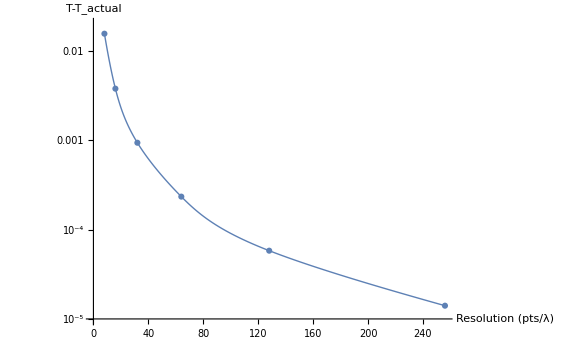

```mathematica
ListLogPlot[Terr,Joined->True,InterpolationOrder->3,AxesLabel->{"Resolution (pts/λ)","T-T_actual"},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotStyle->Thick,PlotMarkers->{Automatic},PlotRange->{10^-5,0.02},ImageSize->Large]
```

```mathematica
0.9199904168589202
```

```mathematica
1/Cos[80°]//N
```

5.75877

```mathematica
Graphics3D[Cuboid[{0,0,0},{1,1,1}]]
```

-Graphics3D-

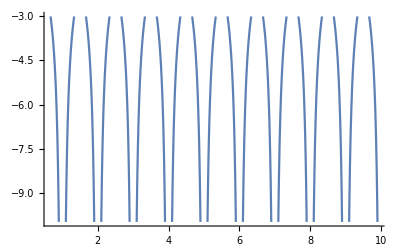

```mathematica
Plot[Table[-1/Abs[x-a],{a,1,10}],{x,0,10},PlotRange->{-3,-10}]
```